# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Kicked LMG

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,F];

Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);

Clear[F];
F[J_,α_,k_,τ_]:=MatrixExp[N[(-I*k/(2J))(Sx[J].Sx[J])]].MatrixExp[(-I*α*τ)(Sz[J])];

Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
Clear[a2iM];
a2iM[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J,2}],20]]
];
Clear[a2im];
a2im[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J+1,J,2}],20]]
];
```

```mathematica
radius=1.99999;
delta=0.025;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
boundaryPoints=(radius)Table[{Cos[i],Sin[i]},{i,0,2Pi,Pi/100}];
circlePoints=Select[gridPoints,Norm[#]<radius&];
region=Join[boundaryPoints,circlePoints];
region//Length
```

20272

```mathematica
radius=0.6;
delta=0.01;
xCoords=Range[-radius,radius,delta];
yCoords=Range[-radius,radius,delta];
gridPoints=Flatten[Table[{x,y},{x,xCoords},{y,yCoords}],1];
region=gridPoints;
region//Length
```

14641

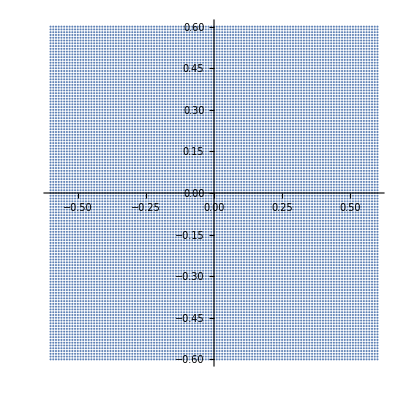

```mathematica
ListPlot[region,AspectRatio->1]
```

```mathematica
J=200;
```

```mathematica
cohesM=ParallelTable[Quiet[a2iM[J,i[[1]],i[[2]]]],{i,region}];
(*cohesm=ParallelTable[Quiet[a2im[J,i[[1]],i[[2]]]],{i,region}];*)
```

```mathematica
(*cohes=ParallelTable[Quiet[a2[J,i[[1]],i[[2]]]],{i,region},DistributedContexts->Full];
cohesfloq=ParallelTable[Conjugate[floqneweigenvec].i,{i,cohes},DistributedContexts->Full];
iprcohesfloq=ParallelTable[Total[Quiet[Abs[i]^4]],{i,cohesfloq}];
data=Table[{region[[i,1]],region[[i,2]],-Log[iprcohesfloq[[i]]]/Log[2J+1]},{i,Length[region]}];
ListDensityPlot[data,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]]<>", ϵ = "<>ToString[epsilon]<>", τ = "<>ToString[N[tau]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]*)
```

## LMG

```mathematica
Clear[Hlmg, floq];
Hlmg[J_]:=Hlmg[J]=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
```

```mathematica
Clear[gx,gy];
gx=-15/10;
gy=1/gx;
```

```mathematica
Clear[lipmatm,lipmatM];
mat2=Hlmg[J];
(*mat2=ConjugateTranspose[rotation].Hlmg[J].rotation;*)
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

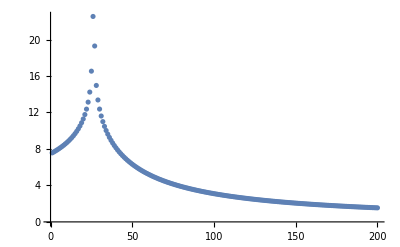

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All]
(*ListPlot[(2Pi)/Differences[Chop[lipeigenvalm]],PlotRange->All]*)
```

```mathematica
d2Mlmg=ParallelTable[Total[Abs[Conjugate[lipeigenvecM].i]^4],{i,cohesM}];
(*d2mlmg=ParallelTable[Total[Abs[Conjugate[lipeigenvecm].i]^4],{i,cohesm}];*)
```

```mathematica
newd2Mlmg=Transpose[{region[[All,1]],region[[All,2]],-Log[d2Mlmg]/Log[J+1]}];
(*newd2mlmg=Transpose[{region[[All,1]],region[[All,2]],-Log[d2mlmg]/Log[J]}];*)
```

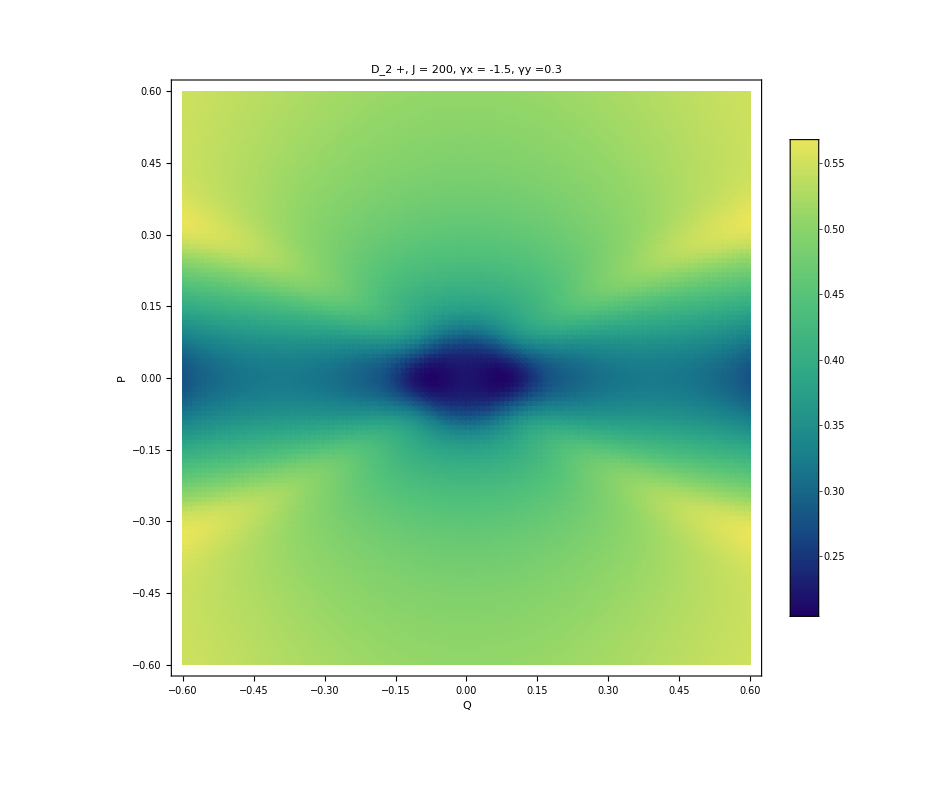

```mathematica
ListDensityPlot[newd2Mlmg,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2 +, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
(*ListDensityPlot[newd2mlmg,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2 -, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]*)
```

## Kicked LMG

```mathematica
Clear[floq];
floq[J_,gx_,gy_,ϵ_,tau_]:=N[MatrixExp[(-I*ϵ)Sz[J]].MatrixExp[-I*tau*Hlmg[J]]];
```

```mathematica
tau=(1/4)Chop[(1/2)(2Pi)/(lipeigenvalM[[18]]-lipeigenvalM[[17]])]
epsilon=(-0.05)tau;
```

1.27616

```mathematica
Clear[mat];
mat=floq[J,gx,gy,epsilon,tau];
(*rotation=MatrixExp[I(N[Pi])Sx[J]];*)
(*mat=ConjugateTranspose[rotation].floq[J,gx,gy,epsilon,tau].rotation;*)
Clear[floqmatm,floqmatM];
floqmatM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
floqmatm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{floqeigenvalM,floqeigenvecM}=Eigensystem[floqmatM];
{floqeigenvalm,floqeigenvecm}=Eigensystem[floqmatm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
floqneweigenvecM=Table[Riffle[floqeigenvecM[[j]],zerosM],{j,J+1}];
floqneweigenvecm=Table[Riffle[zerosm,floqeigenvecm[[j]]],{j,J}];
floqneweigenvec=Riffle[floqneweigenvecM,floqneweigenvecm];
floqneweigenval=Riffle[floqeigenvalM,floqeigenvalm];
```

```mathematica
d2M=ParallelTable[Total[Abs[Conjugate[floqeigenvecM].i]^4],{i,cohesM}];
(*d2m=ParallelTable[Total[Abs[Conjugate[floqeigenvecm].i]^4],{i,cohesm}];*)
```

```mathematica
newd2M=Transpose[{region[[All,1]],region[[All,2]],-Log[d2M]/Log[J+1]}];
(*newd2m=Transpose[{region[[All,1]],region[[All,2]],-Log[d2m]/Log[J]}];*)
```

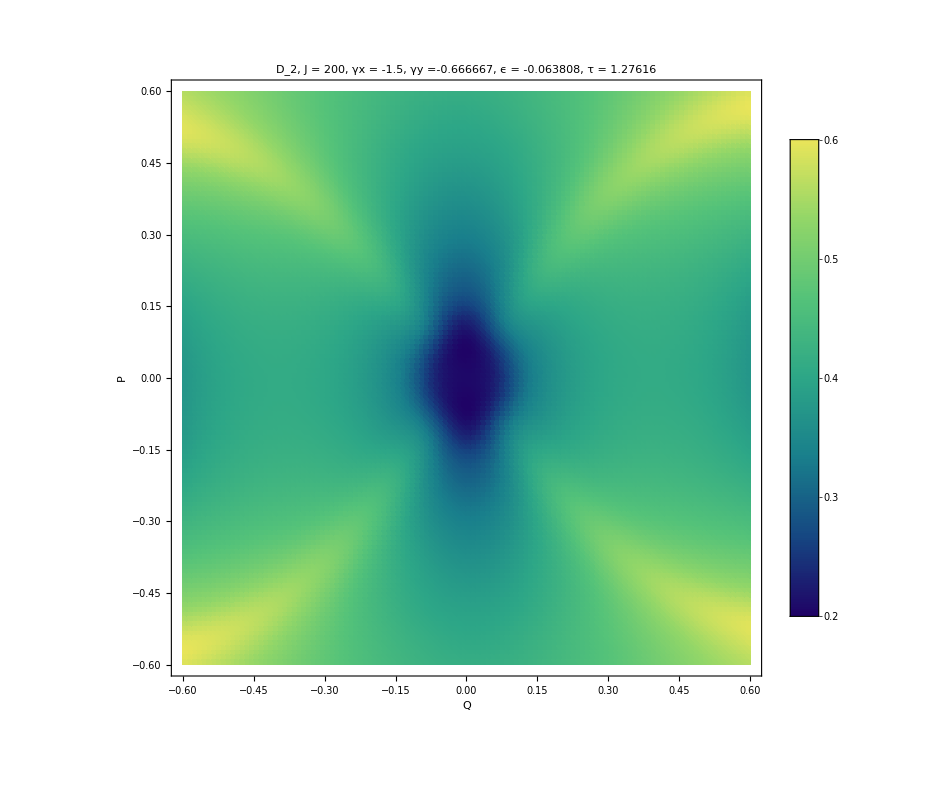

```mathematica
ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]]<>", ϵ = "<>ToString[N[epsilon]]<>", τ = "<>ToString[N[tau]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

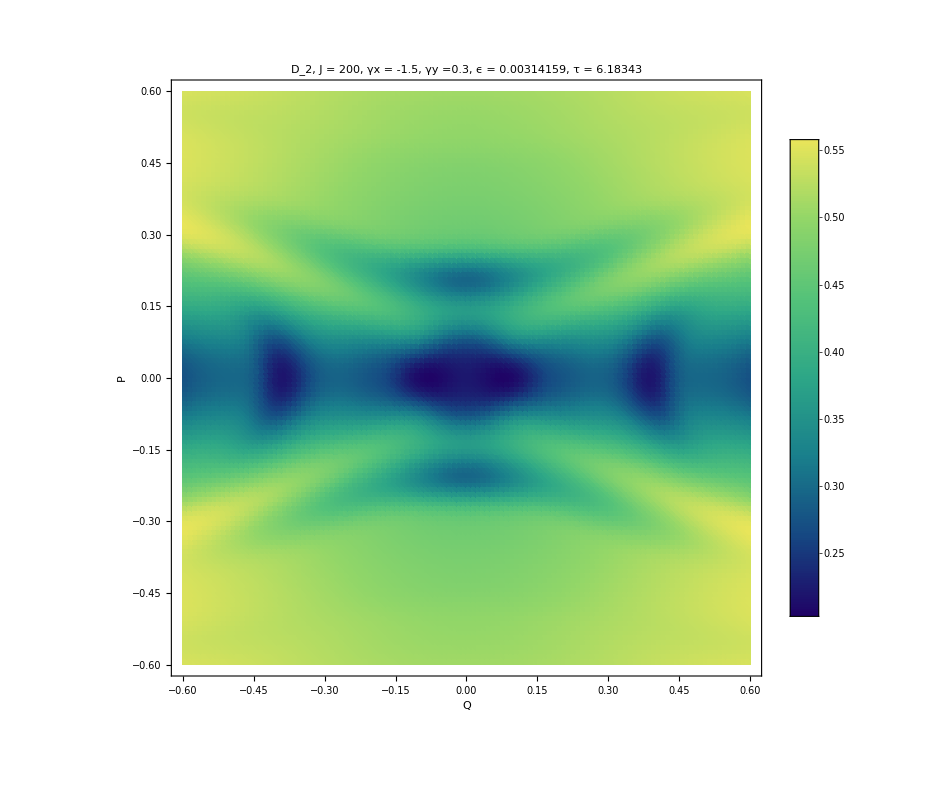

```mathematica
ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]]<>", ϵ = "<>ToString[epsilon]<>", τ = "<>ToString[N[tau]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
```

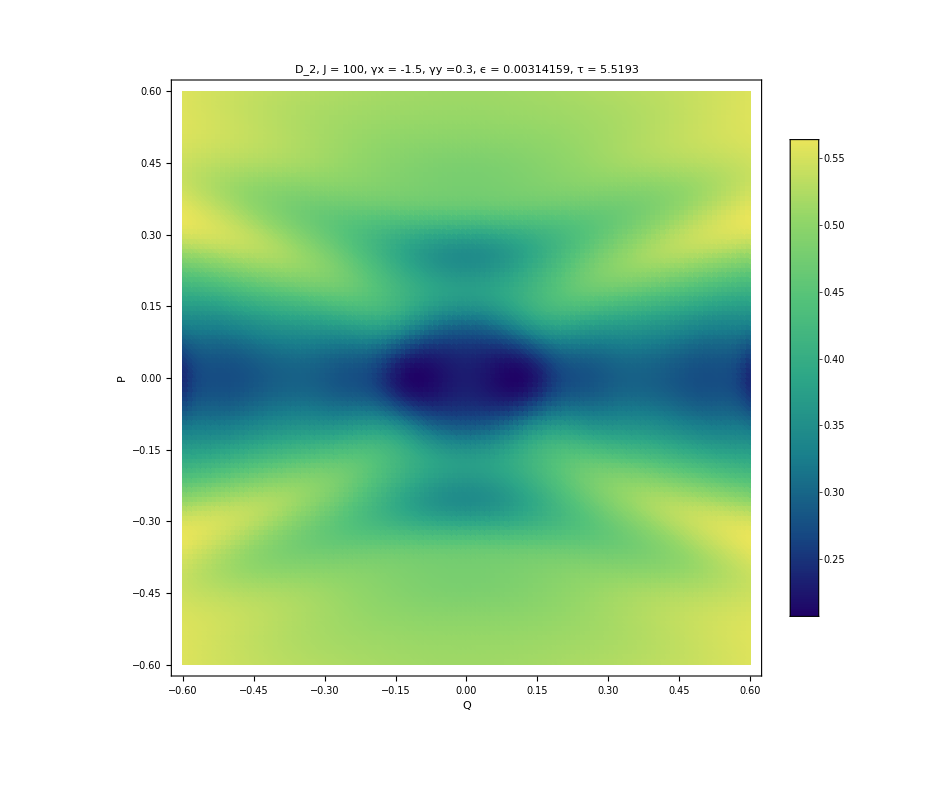

```mathematica
ListDensityPlot[newd2M,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]]<>", ϵ = "<>ToString[epsilon]<>", τ = "<>ToString[N[tau]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]
(*ListDensityPlot[newd2m,PlotRange->All,PlotTheme->"Detailed",ColorFunction->"BlueGreenYellow",PlotLabel->Style["D_2, J = "<>ToString[J]<>", γx = "<>ToString[N[gx]]<>", γy ="<>ToString[N[gy]]<>", ϵ = "<>ToString[epsilon]<>", τ = "<>ToString[N[tau]],25,Black],ImageSize->800,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True]*)
```

```mathematica
h0=ParallelTable[Chop[Conjugate[i].lipmatM.i],{i,floqeigenvecM}];
```

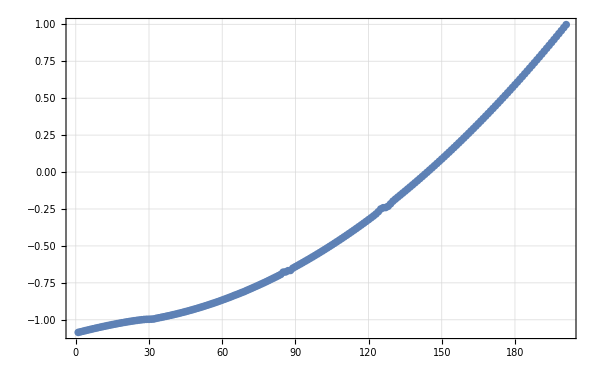

```mathematica
ListPlot[Sort[h0]/J,PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

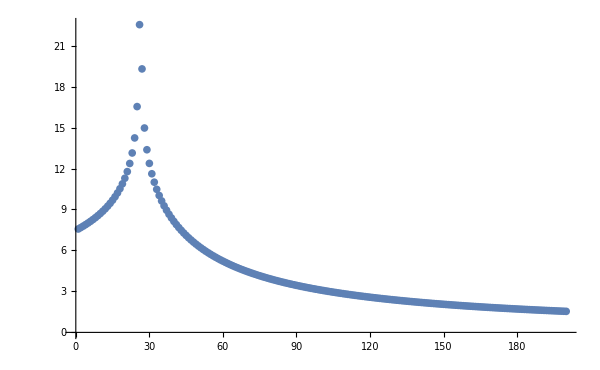

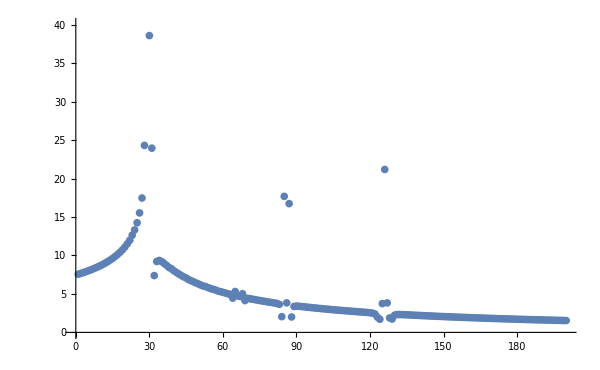

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All,ImageSize->600]
ListPlot[2Pi/Differences[Sort[h0]],ImageSize->600,PlotRange->{All,{0,40}}]
```

-Graphics-

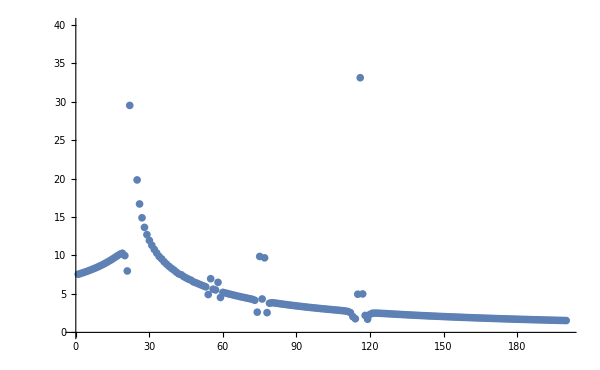

```mathematica
ListPlot[(2Pi)/Differences[Chop[lipeigenvalM]],PlotRange->All,ImageSize->600]
ListPlot[2Pi/Differences[Sort[h0]],ImageSize->600,PlotRange->{All,{0,40}}]
```

## Husimis

```mathematica
Clear[husimiM,husimim];
husimiM[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesM[[i]]].ψ]^2},{i,Length[region]}];
husimim[ψ_]:=ParallelTable[{region[[i,1]],region[[i,2]],Abs[Conjugate[cohesm[[i]]].ψ]^2},{i,Length[region]}];
```

```mathematica
Do[

Export["northeigenvecMas_"<>ToString[i]<>"_J_"<>ToString[J]<>"_alpha_"<>ToString[N[α]]<>"_k_"<>ToString[k]<>"_dq_"<>ToString[delta]<>".png",ListDensityPlot[husimiM[sortedeigenvecM[[i]]],PlotRange->{All,All,{0,1}},PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["North Eigenvec +"<>ToString[i]<>", J = "<>ToString[J]<>", α = "<>ToString[N[α]]<>", k = "<>ToString[k]<>", dq = "<>ToString[delta],25,Black],FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Frame->True,ImageSize->1000,ColorFunction->"BlueGreenYellow"]]

,{i,J+1}]
```

# <r>

```mathematica
Clear[Hlmg, floq];
Hlmg[J_,gx_,gy_]:=N[(gy/(2J-1))(Sy[J].Sy[J])+(gx/(2J-1))(Sx[J].Sx[J])+(Sz[J])];
floq[J_,gx_,gy_,ϵ_,tau_]:=N[MatrixExp[(-I*ϵ)Sz[J]].MatrixExp[-I*tau*Hlmg[J,gx,gy]]];
```

```mathematica
Clear[gx,gy,epsilon];
gx=-5/10;
gy=-3/10;
tau=5.0;
J=200;
```

```mathematica
Clear[mat2,mat];
mat2=Hlmg[N[J],gx,gy];
Clear[lipmatm,lipmatM];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
lipmatM=Table[mat2[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
lipmatm=Table[mat2[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{lipeigenvalM,lipeigenvecM}=Transpose[Sort[Transpose[Eigensystem[lipmatM]]]];
{lipeigenvalm,lipeigenvecm}=Transpose[Sort[Transpose[Eigensystem[lipmatm]]]];
lipneweigenvecM=Table[Riffle[lipeigenvecM[[j]],zerosM],{j,J+1}];
lipneweigenvecm=Table[Riffle[zerosm,lipeigenvecm[[j]]],{j,J}];
lipneweigenvec=Riffle[lipneweigenvecM,lipneweigenvecm];
lipneweigenval=Chop[Riffle[lipeigenvalM,lipeigenvalm]];
```

```mathematica
2*Pi*lipneweigenval[[1]]/J
```

-6.28962

```mathematica
mat=floq[N[J],gx,gy,epsilon,tau];
Clear[floqmatm,floqmatM];
floqmatM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
floqmatm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{floqeigenvalM,floqeigenvecM}=Eigensystem[floqmatM];
{floqeigenvalm,floqeigenvecm}=Eigensystem[floqmatm];
floqneweigenvecM=Table[Riffle[floqeigenvecM[[j]],zerosM],{j,J+1}];
floqneweigenvecm=Table[Riffle[zerosm,floqeigenvecm[[j]]],{j,J}];
floqneweigenvec=Riffle[floqneweigenvecM,floqneweigenvecm];
floqneweigenval=Riffle[floqeigenvalM,floqeigenvalm];
```